# Economics of AI

```mathematica
prod[x_]:=Apply[Times,Flatten[{x},Infinity]]

maxPairIndex[x_List]:=Module[{pairsWithIndices,maxPairWithIndex,indices, newx},
 newx= Map[prod,x]; 
pairsWithIndices=MapIndexed[{#2[[1]],#1}&,Partition[newx,2,1]];
maxPairWithIndex=First@MaximalBy[pairsWithIndices,Total@Last@#&];
indices=maxPairWithIndex[[1]];
indices]
```

```mathematica
replaceWithPair[x_List,index_Integer]:=Module[{q1,q2,condition,newList,result,newx},
newx = x; 
q1=prod[x[[index]]];
q2=prod[x[[index+1]]];
condition=1/q1+1/q2>1/(q1*q2);
result = If[condition,newList=ReplacePart[newx,index->{x[[index]],x[[index+1]]}];
Delete[newList,index+1],newx];
result
]
```

```mathematica
OptimalSplit[x_]:=Module[{maxindex,newx},
maxindex = maxPairIndex[x];
newx = replaceWithPair[x,maxindex];
If[newx===x,x,OptimalSplit[newx]]
]
```

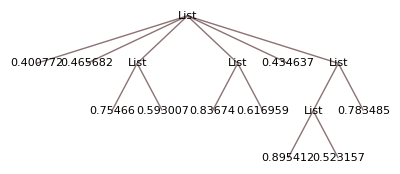

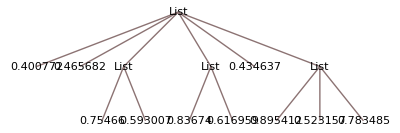

```mathematica
lower = 0.4; 
n = 10; 
x =Table[Random[UniformDistribution[{lower,1}]],{n}] ;
TreeForm[OptimalSplit[x]]
TreeForm[Map[If[ListQ[#],Flatten[#,Infinity],#]&,OptimalSplit[x]]]
```

```mathematica
tree=Map[Round[#,0.001]&,tree,{-1}];
tree=ReplaceAll[tree,List->"."];
```

```mathematica
tree=OptimalSplit[x]
```

{0.400772,0.465682,{0.75466,0.593007},{0.83674,0.616959},0.434637,{{0.895412,0.523157},0.783485}}

{0.400772,0.465682,{0.75466,0.593007},{0.83674,0.616959},0.434637,{0.895412,0.523157,0.783485}}

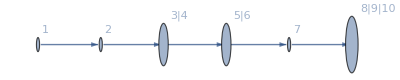

```mathematica
flatTree[x_]:=Map[If[ListQ[#],Flatten[#,Infinity],#]&,OptimalSplit[x]];
names[x_]:=Flatten[MapIndexed[{# ->#2[[1]]}&,Flatten[x,Infinity]]]
flattTree=Map[If[ListQ[#],Flatten[#,Infinity],#]&,OptimalSplit[x]]
repr[x_List]:=StringJoin[Riffle[ToString/@Flatten[x,Infinity],"|"]];
repr[x_?NumericQ]:= ToString[x]
pairs=flattTree/.names[x];
labels=Map[#->repr[#]&,pairs];
cost=Map[Round[#,0.01]&,Map[Apply[Times,#]&,flattTree]];
edges =Map[#[[1]]->#[[2]]&,Partition[flattTree/.names[x],2,1]];
Graph[edges,
VertexLabels->labels,
VertexSize->Map[#->(Length[#]+1)/20&,pairs]
]
```

```mathematica
q1=3/5;
q2 = 4/5;
cm  = 1; 
ch = 3/2
```

3/2

```mathematica
cm/q1//N
```

1.66667

Suppose the first task has success probability q1 .
It can be down by hand with probability ch.
The second task has success probability q2.
It cannot be done by hand. 
There is a common management cost, cm the same for both.

Cheaper to do first task by hand :

Do first by hand, automate second :

```mathematica
ch + cm/q2
```

11/4

Automate both :

```mathematica
cm/(q1*q2)
```

```mathematica
ClearAll[partitions];
partitions[list_List]/;Length[list]>0:=Flatten[Table[Map[Prepend[#1,Take[list,i]]&,partitions[Drop[list,i]]],{i,Length[list]}],1]
partitions[_]:={{}}
```

```mathematica
PrettyPrint[{{1,2,3}}]
```

```mathematica
PrettyPrint[x_]:=StringJoin[Riffle[Map[If[ListQ[#] && Length[#]>1,"["<>StringJoin[ToString/@Riffle[#,"|"]]<>"]",ToString[#]]&,x],"."]]
```

```mathematica
PrettyPrintRecursive[x_?ListQ]:=If[AllTrue[x,NumericQ],"["<>ToString/@Riffle[x,"|"]<>"]",Map[PrettyPrintRecursive[#]&,x]];
PrettyPrint[x_]:=StringJoin[ToString/@PrettyPrintRecursive[x]]
```

```mathematica
printSingle[x_]:=If[Total[(x/.hRules)] >Total[(cm/(x/.qRules))],"[" <> ToString[x[[1]]]<>"]",ToString[x[[1]]]]
```

```mathematica
Clear[Sim]
```

```mathematica
OptimalSplit[Q_,CH_,cm_]:=Module[{},
P = partitions[Range[Length[Q]]];
MachineCost[x_?List]:=Apply[Times,Q[[x]];
CostSegment[x_]:=If[Length[x]>1,cm/Apply[Times,Q[[x]]],
Min[{CH[[x[[1]]]], cm/Q[[x[[1]]]]}]];
(*Map[CostSegment,x];*)
P
]
```

```mathematica
OptimalSplit[{0.4, 0.8},{1,1}, 1]
```

{{{1},{2}},{{1,2}}}

```mathematica
Q = {0.5, 0.5};
CH = {1,1};
cm = 1;
P = partitions[Range[Length[Q]]];
MachineCost[x_?ListQ]:=cm/Apply[Times,Q[[x]]];
HumanCost[x_]:=Total[CH[[x]]];
CostSegment[x_]:=If[Length[x]>1,MachineCost[x],Min[{HumanCost[x],MachineCost[x]}]];
Cost[x_]:=Total[Map[CostSegment,x]]
costs = Map[Cost,P]
BestPartition = Last[First[Sort[Transpose[{costs,P}]]]];
```

{2,4.}

```mathematica
LabelSegment[x_]:=If[Length[x]>1, Table["M", Length[x]], If[(x[[1]]/.hRules)< (cM/(x[[1]]/.qRules)),"H", "M"]];
DoerCostSegment[x_]:=If[Length[x]>1,0,If[(x[[1]]/.hRules)< (cM/(x[[1]]/.qRules)),(x[[1]]/.hRules),0]];
ManagerCostSegment[x_]:=If[Length[x]>1,cM/Apply[Times,x/.qRules],If[(x[[1]]/.hRules)< (cM/(x[[1]]/.qRules)),0,(cM/(x[[1]]/.qRules))]];
```

```mathematica
BestPartition
```

{{1},{2}}

```mathematica
Sim[n_,lowerbound_,chlow_,chhigh_,cM_]:=Module[{
P,Q,qRules,cH,hRules,CostSegment,Cost,costs, labels,together,BestPartition
},
P = partitions[Range[n]];
Q=Table[Random[UniformDistribution[{lowerbound,1}]],{n}];
qRules = Flatten[MapIndexed[{#2[[1]]->#}&,Q]];
cH = Table[Random[UniformDistribution[{chlow,chhigh}]],{n}]; 
hRules = Flatten[MapIndexed[{#2[[1]]->#}&,cH]];
CostSegment[x_]:=If[Length[x]>1,cM/Apply[Times,x/.qRules],Min[{x[[1]]/.hRules, cM/(x[[1]]/.qRules)}]];
Cost[x_]:=Total@Map[CostSegment,x];
costs = Map[Cost, P];
labels = Map[PrettyPrint,Map[If[Length[#]==1,#[[1]],#]&,P]];
together =Transpose[Sort[ Transpose[{costs, labels}]]];
BarChart[together[[1]],ChartLabels->together[[2]],BarOrigin->Left];
BestPartition = Last[First[Sort[Transpose[{costs,P}]]]];
LabelSegment[x_]:=If[Length[x]>1, Table["M", Length[x]], If[(x[[1]]/.hRules)< (cM/(x[[1]]/.qRules)),"H", "M"]];
DoerCostSegment[x_]:=If[Length[x]>1,0,If[(x[[1]]/.hRules)< (cM/(x[[1]]/.qRules)),(x[[1]]/.hRules),0]];
ManagerCostSegment[x_]:=If[Length[x]>1,cM/Apply[Times,x/.qRules],If[(x[[1]]/.hRules)< (cM/(x[[1]]/.qRules)),0,(cM/(x[[1]]/.qRules))]];
doerCost = Total@Map[DoerCostSegment,BestPartition];
managerCost = Total@Map[ManagerCostSegment, BestPartition];
frac = doerCost/(managerCost + doerCost);
{
"Q"->Q, 
"cH"->cH, 
"machineCost"->cM/Q, 
"best"->BestPartition, 
"bestPP"->PrettyPrint[BestPartition],
"By-task assignment"->Map[LabelSegment,BestPartition], 
"segementCosts"->Map[CostSegment,BestPartition],
"TotalCost"->Cost[BestPartition],
"doerCost"-> doerCost,
"fracDoerCost"->frac
}
]
```

```mathematica
TableForm[Sim[n=5,lowerbound=0.2,chlow = 2,chhigh = 3,cM = 1]]
```

```mathematica
{{"Q"->{0.8502932113040944,0.8047214149623931,0.9084799955482945,0.27489596549852346,0.5652334182442373}}, {"cH"->{2.806184627937651,2.7442057721963415,2.0006254284853284,2.758737856453662,2.9751685382401694}}, {"machineCost"->{1.1760648993848843,1.2426660722664287,1.1007397024702459,3.637739819813293,1.7691806034863637}}, {"best"->{{1,2,3},{4},{5}}}, {"bestPP"->"[1|2|3][4][5]"}, {"By-task assignment"->{{"M","M","M"},"H","M"}}, {"segementCosts"->{1.6086825867497447,2.758737856453662,1.7691806034863637}}, {"TotalCost"->6.136601046689771}, {"doerCost"->2.758737856453662}, {"fracDoerCost"->0.4495547022633631}}
```

```mathematica
sampleSize = 1000
```

1000

### Mangement Costs

```mathematica
s1 =Table[Sim[n=5,lowerbound=0.2,chlow = 2,chhigh = 3,cM = 0.8],{sampleSize}];
s2=Table[Sim[n=5,lowerbound=0.2,chlow = 2,chhigh = 3,cM = 1.1*0.8],{sampleSize}];
{x1,x2}={Mean[Map["TotalCost"/.#&,s1]],Mean[Map["TotalCost"/.#&,s2]]}
100*(x2-x1)/x1
```

```mathematica
cManagement = {0.1,0.5, 0.75, 1, 1.25, 1.5,2, 4};
costs =Map[Mean[Table["TotalCost"/.Sim[n=5,lowerbound=0.2,chlow = 2,chhigh = 3,cM = #],{sampleSize}]]&,cManagement]
```

{0.855027,4.27622,6.06223,7.37558,8.49764,9.12691,10.4685,12.2734}

```mathematica
cM = {0.5, 0.75, 1, 1.25, 1.5};
```

```mathematica
{cM,costs}
```

{{0.5,0.75,1,1.25,1.5},{4.28493,6.01258,7.42153,8.49681,9.27068}}

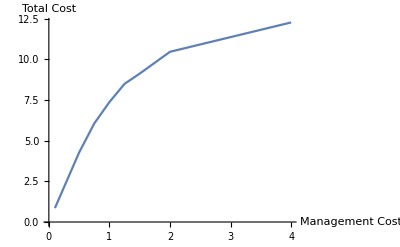

```mathematica
ListPlot[Transpose[{cManagement,costs}],Joined->True,AxesLabel->{"Management Cost", "Total Cost"}]
```

Claim: With more complex chains, total costs are more sensitive to changes in the cost of management.

```mathematica
qL = {0.1,0.2, .5, 0.75, 0.9};
costs =Map[Mean[Table["TotalCost"/.Sim[n=5,lowerbound=#,chlow = 2,chhigh = 3,cM =1],{sampleSize}]]&,qL]
```

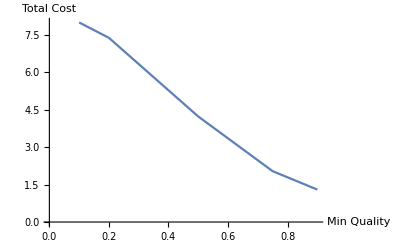

```mathematica
ListPlot[Transpose[{qL,costs}],Joined->True,AxesLabel->{"Min Quality", "Total Cost"}]
```

```mathematica
s1 =Table[Sim[n=6,lowerbound=0.2,chlow = 2,chhigh = 3,cM = 0.8],{sampleSize}];
s2=Table[Sim[n=6,lowerbound=0.2,chlow = 2,chhigh = 3,cM = 1.1*0.8],{sampleSize}];
{x1,x2}={Mean[Map["TotalCost"/.#&,s1]],Mean[Map["TotalCost"/.#&,s2]]}
100*(x2-x1)/x1
```

{7.61391,8.21072}

7.83844

```mathematica
{x1,x2}={Mean[Map["fracDoerCost"/.#&,s1]],Mean[Map["fracDoerCost"/.#&,s2]]}
100*(x2-x1)/x1
```

{0.230327,0.280797}

21.9125

8.22038

8.21405

```mathematica
7*1.2
```

8.4

```mathematica
{"frac"->0.8315362892589279,"doerCost"->6.70608850678268,"best"->{{1},{2},{3},{4},{5}},"Q"->{0.42683756526655353,0.06205816177266045,0.7360470281328707,0.30650333612172614,0.15520751535220803},"cH"->{1.2004385338430341,1.9482335229352628,1.859768124487271,1.6065982805897172,1.9508181694146658},"machineCost"->{2.3428116018221483,16.11391590462074,1.3586088412539323,3.262607228532271,6.4429869760541445},{"H","H","NA","H","H"},"segementCosts"->{1.2004385338430341,1.9482335229352628,1.3586088412539323,1.6065982805897172,1.9508181694146658}}
```

{frac→0.831536,doerCost→6.70609,best→{{1},{2},{3},{4},{5}},Q→{0.426838,0.0620582,0.736047,0.306503,0.155208},cH→{1.20044,1.94823,1.85977,1.6066,1.95082},machineCost→{2.34281,16.1139,1.35861,3.26261,6.44299},{H,H,NA,H,H},segementCosts→{1.20044,1.94823,1.35861,1.6066,1.95082}}

```mathematica
fracSim=Table[Sim,{20000}]
```

{0.583718,0.251156,19996,0.411251,0.378186}
 |  |  |  |

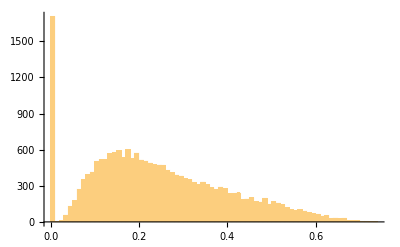

0.557902

```mathematica
Histogram[fracSim,{0.01}]
```

```mathematica
First[together[[2]]]
```

[1][2][3|4|5]

First::nofirst: {} has zero length and no first element.

$Aborted

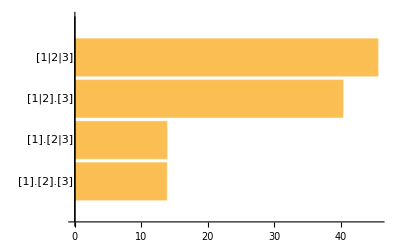

```mathematica
OptimalSplit[Q]
```

```mathematica
Cost[{1,2,3,4,5}]
```

4.09248

2.1507

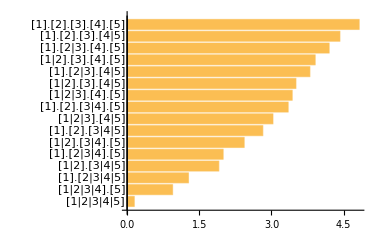

```mathematica
1/CostSegment[{1,2,3,4,5}]
```

```mathematica
P = partitions[{1,2,3,4,5}]
```

{{{1},{2},{3},{4},{5}},{{1},{2},{3},{4,5}},{{1},{2},{3,4},{5}},{{1},{2},{3,4,5}},{{1},{2,3},{4},{5}},{{1},{2,3},{4,5}},{{1},{2,3,4},{5}},{{1},{2,3,4,5}},{{1,2},{3},{4},{5}},{{1,2},{3},{4,5}},{{1,2},{3,4},{5}},{{1,2},{3,4,5}},{{1,2,3},{4},{5}},{{1,2,3},{4,5}},{{1,2,3,4},{5}},{{1,2,3,4,5}}}

```mathematica
P[[1]]
```

{{1},{2},{3},{4},{5}}

```mathematica
M[1,2,3]
```

M[1,2,3]

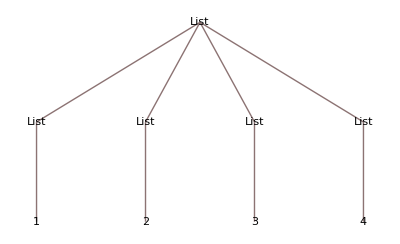
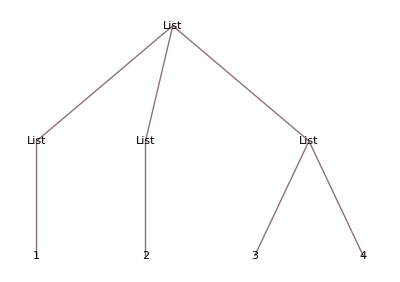
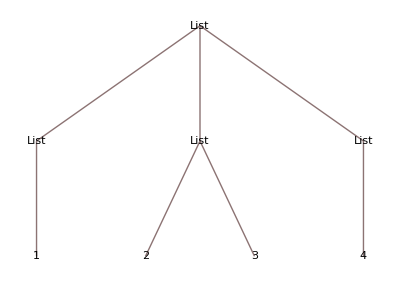
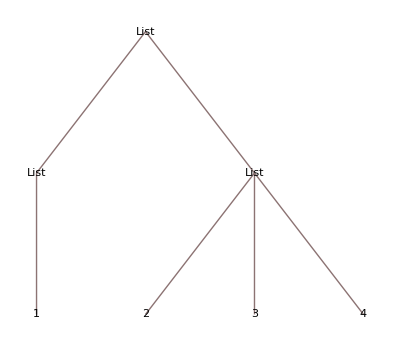
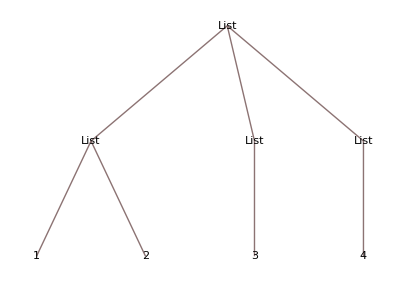
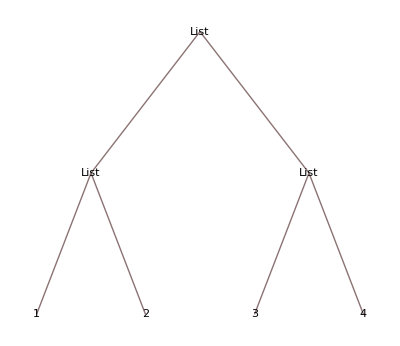
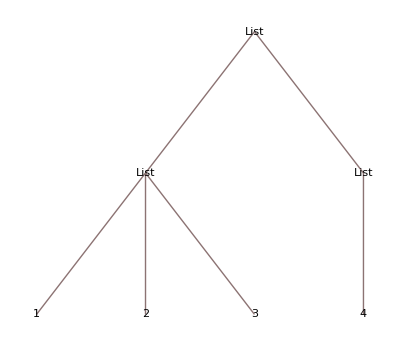
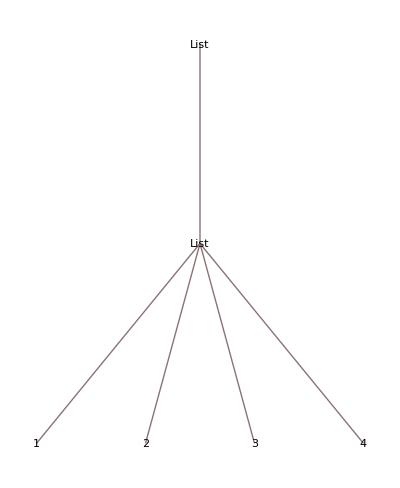

```mathematica
Map[TreeForm, partitions[{1,2,3,4}]]
```

```mathematica
ch < cm/q1
```

True

```mathematica
cm/(q1*q2) < ch + cm/q2
```

True

```mathematica
?Graph
```

```mathematica
Apply[Times,Map[Subscript[q,#]&,{1,2,3,4}]]
```

q_1 q_2 q_3 q_4

```mathematica
ToString[Subscript[q, 1] Subscript[q, 2] Subscript[q, 3] Subscript[q, 4],InputForm]
```

Subscript[q, 1]*Subscript[q, 2]*Subscript[q, 3]*Subscript[q, 4]

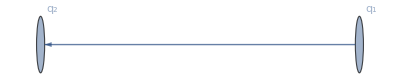

```mathematica
Graph[1->2,VertexLabels->{1->Subscript[q,1],2->Subscript[q,2]}]
```

```mathematica
?TreeForm
```

```mathematica
s=OptimalSplit[x]
```

{{{0.904713,{0.637493,0.908884}},0.621624},{0.449995,{0.865563,0.657803}},{0.605919,{0.930593,0.776779}}}

```mathematica
r =Flatten[MapIndexed[{#1->#2[[1]]}&,Flatten[s,Infinity]]]
```

{0.904713→1,0.637493→2,0.908884→3,0.621624→4,0.449995→5,0.865563→6,0.657803→7,0.605919→8,0.930593→9,0.776779→10}

```mathematica
Join[{1,3},{2,3}]
```

{1,3,2,3}

```mathematica
containsList[x_]:=MemberQ[x,_List];
```

```mathematica
StringJoin[ToString/@{1,2,3}]
```

123

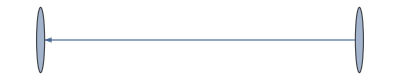

```mathematica
Graph[{"a"->"b"}]
```

```mathematica
drawLeaf[parent_, children_]:=Module[{},
first = Map[parent->repr[#]&,children];
second = Map[If[containsList[#],drawLeaf[repr[#],#],Null]&,children];
DeleteCases[Join[first,second], Null]
]
```

```mathematica
drawLeaf["Root",{1,{2,{3,9}}}]
```

{239→2,239→39,{239→2,239→39}}

```mathematica
Graph[Flatten[drawLeaf["Root",{1,{2,{3,9}}}],Infinity]]
```

-Graphics-

```mathematica
z=drawLeaf["root",e]
```

{{root→{{{{{1, {2, 3}}, 4}, {5, {6, 7}}, {8, {9, 10}}}→{{{{1, {2, 3}}, 4}→{1, {2, 3}}→1},{{{1, {2, 3}}, 4}→{{{1, {2, 3}}→{2, 3}→2},{{1, {2, 3}}→{2, 3}→3}}}}},{{{{1, {2, 3}}, 4}, {5, {6, 7}}, {8, {9, 10}}}→{{1, {2, 3}}, 4}→4}}},{root→{{{{{1, {2, 3}}, 4}, {5, {6, 7}}, {8, {9, 10}}}→{5, {6, 7}}→5},{{{{1, {2, 3}}, 4}, {5, {6, 7}}, {8, {9, 10}}}→{{{5, {6, 7}}→{6, 7}→6},{{5, {6, 7}}→{6, 7}→7}}}}},{root→{{{{{1, {2, 3}}, 4}, {5, {6, 7}}, {8, {9, 10}}}→{8, {9, 10}}→8},{{{{1, {2, 3}}, 4}, {5, {6, 7}}, {8, {9, 10}}}→{{{8, {9, 10}}→{9, 10}→9},{{8, {9, 10}}→{9, 10}→10}}}}}}

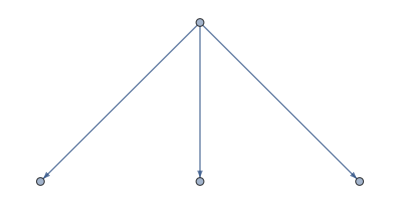

```mathematica
Graph[Flatten[z,Infinity]]
```

```mathematica
Map[ListQ,s]
```

{True,True,True}

{0.34234→0.23423}

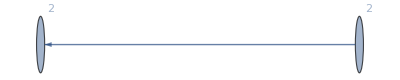

```mathematica
a = {0.34234 ->0.23423}
Graph[a, VertexLabels->{}]
```

```mathematica
?VertexLabels
```

```mathematica
?Graph
```

```mathematica
OptimalSplit[Table[0.9, {10}]]
```

First::nofirst: {} has zero length and no first element.

$Aborted

```mathematica
TreeForm[OptimalSplit[]]
```

First::nofirst: {} has zero length and no first element.

$Aborted

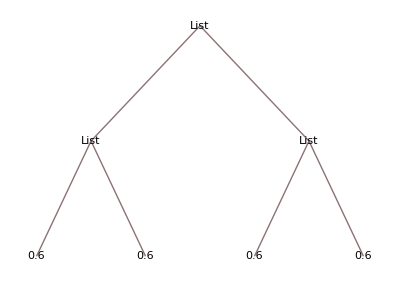

```mathematica
TreeForm[OptimalSplit[{0.6, 0.6, 0.6, 0.6}]]
```

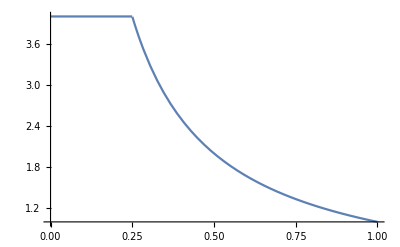

```mathematica
Plot[Min[{4,1/q}], {q, 0,1}]
```

```mathematica
Cases[{{2.3,23,.23}},{__?NumericQ},Infinity]
```

{{2.3,23,0.23}}

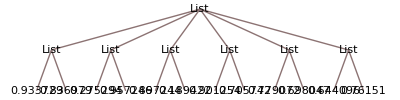

```mathematica
extractedList=Cases[OptimalSplit[x],{__?NumericQ},Infinity];
TreeForm[extractedList]
```

```mathematica
extractedList
```

{{0.933729,0.836979},{0.275294,0.957246},{0.897244,0.189422},{0.901254,0.705742},{0.779072,0.698047},{0.644096,0.76151}}

```mathematica
flattenList[x_List]:=Flatten[Map[If[ListQ[#],flattenList[#],#]&,x]];
flattenList[x_?NumberQ]:=x;
```

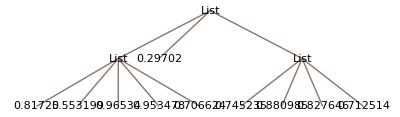

{1,2}

```mathematica
TreeForm[Map[If[ListQ[#],Flatten[#,Infinity],#]&,OptimalSplit[x]]]
```

```mathematica
flattenList[OptimalSplit[x]]
```

{0.81725,0.553199,0.96534,0.953478,0.706624,0.29702,0.745235,0.880985,0.827646,0.712514}

```mathematica
x
```

{0.81725,0.553199,0.96534,0.953478,0.706624,0.29702,0.745235,0.880985,0.827646,0.712514}

```mathematica
OptimalSplit[x]
```

{{{0.81725,0.553199},{{0.96534,0.953478},0.706624}},0.29702,{{0.745235,{0.880985,0.827646}},0.712514}}

```mathematica
makeTree[OptimalSplit[x]]
```

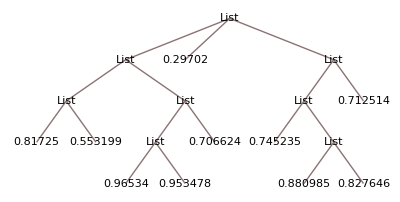

```mathematica
TreeForm[OptimalSplit[x]]
```

```mathematica
Flatten[OptimalSplit[x],1]
```

{{0.81725,0.553199},{{0.96534,0.953478},0.706624},0.29702,{0.745235,{0.880985,0.827646}},0.712514}

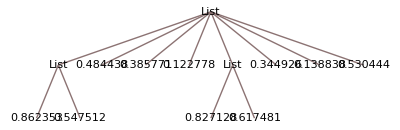

```mathematica
TreeForm[OptimalSplit[x]]
```

```mathematica
tree=Map[Round[#,0.001]&,tree,{-1}];
tree=ReplaceAll[tree,List->"."];
```

```mathematica
tree
```

.[.[.[.[0.576],.[0.354]],.[0.792,0.949,0.79,0.677]],.[.[0.451],.[0.472,0.749,0.74]]]

```mathematica
treeForm = TreeForm[tree]
```

```mathematica
Rule@@@Level[treeForm,{-2}]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

{Rule[0.576324],Rule[0.354292],Rule[0.792196,0.948907,0.790016,0.677212],Rule[0.451428],Rule[0.472046,0.748582,0.74017]}

```mathematica
treeList=Level[treeForm,{-2},"VertexNames"->True,"Edges"->True];
```

Level::optx: Unknown option VertexNames in ….

```mathematica
treeRules=Rule@@@treeList;
```

```mathematica
treeList=Level[treeForm,{-2},"VertexNames"->True,"Edges"->True];
treeRules=Rule@@@treeList;
```

```mathematica
MinCost[lowerbound_,n_]:=Module[{},
x =Table[Random[UniformDistribution[{lowerbound,1}]],{n}] ;
tree = RecursiveSplit[x];
extractedList=If[tree === Flatten[tree, Infinity],Cost[tree],Total[Cost/@Cases[tree,{__?NumericQ},Infinity]]]
]
```

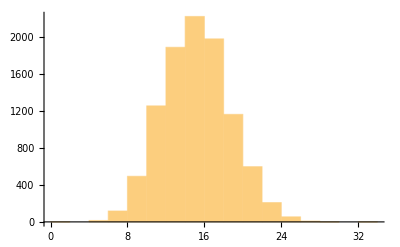

```mathematica
Histogram[Table[MinCost[0.25,10],{10000}]]
```

```mathematica
Cost[{1,1,1}]
```

1

```mathematica
LB = Table[0.01 + i/100, {i,0,90}];
avg = Map[AvgCost[#,10]&,LB];
avg20 = Map[AvgCost[#,20]&,LB];
```

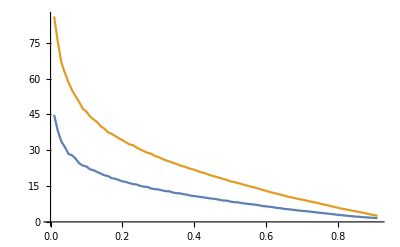

```mathematica
ListPlot[{Transpose[{LB,avg}],Transpose[{LB, avg20}]},Joined->True]
```

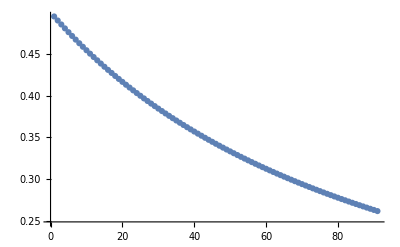

```mathematica
ListPlot[1/(1+LB)/2]
```

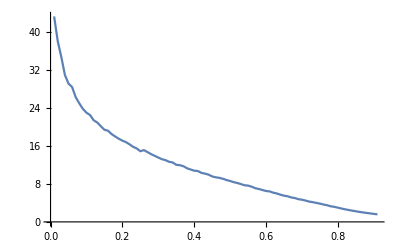

```mathematica
ListPlot[Transpose[{LB,avg}],Joined->True]
```

```mathematica
-Graphics-Plot
```

```mathematica
x =Table[Random[UniformDistribution[{.9,1}]],{10}] ;
tree = RecursiveSplit[x];
```

```mathematica
AvgCost[lb_, n_]:=Mean[Table[MinCost[lb,n],{1000}]]
```

```mathematica
x =Table[Random[UniformDistribution[{.4,1}]],{10}] ;
tree = RecursiveSplit[x];
extractedList=Cases[tree,{__?NumericQ},Infinity];
Tally[Length/@extractedList]
```

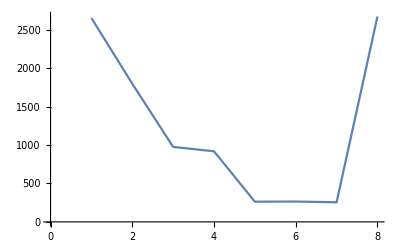
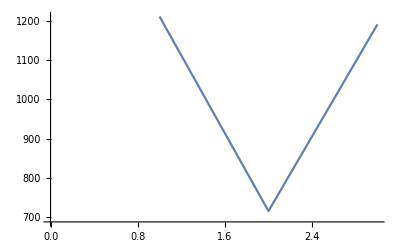

```mathematica
Map[CostPlot,SplitAt[x,8]]
```

```mathematica
smallestIndex[SplitAt[x,8][[1]]]
```

8

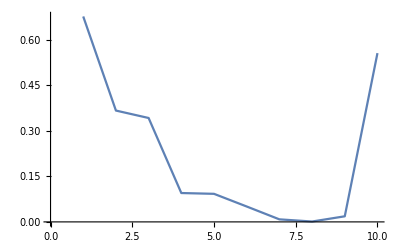

```mathematica
ListPlot[g[x],Joined->True]
```

```mathematica
f[x_]:=FoldList[Times, First[x], Rest[x]]; 
g[x_]:=f[x]+Reverse[f[Reverse[x]]] (*Finds the cut point*)
```

```mathematica
Cost[x_]:=1 /Apply[Times,x]
smallestIndex[x_]:=Ordering[x][[1]]
SplitAt[x_,i_]:={x[[;;i]],x[[i+1;;]]};
PotentialCosts[x_]:=Table[Total@(Cost/@SplitAt[x,i]),{i,1,Length[x]}];
CandidateSplit[x_]:=SplitAt[x,smallestIndex[PotentialCosts[x]]]
OptimalSplit[x_]:=Module[{basecost, candidate, splitcost},
basecost = Cost[x];
candidate = CandidateSplit[x];
splitcost = Total[Map[Cost, candidate]];
If[basecost <splitcost, x, candidate]
];
RecursiveSplit[x_]:=Module[{BaseCost, SplitCost},
If[x === OptimalSplit[x], x, Map[RecursiveSplit,OptimalSplit[x]]]
]
```

```mathematica
OptimalSplit[{0.9, 0.9,0.1,0.1, 0.2, 0.7}]
```

```mathematica
RecursiveSplit[x_]:=Module[{BaseCost, SplitCost},
If[x === OptimalSplit[x], x, Map[RecursiveSplit,OptimalSplit[x]]]
]
```

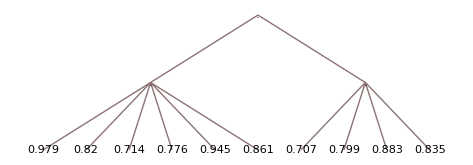

GraphicsGrid::list: … is not a list of lists.

```mathematica
x =Table[Random[UniformDistribution[{.7,1}]],{10}] ;
tree = RecursiveSplit[x];
tree=Map[Round[#,0.001]&,tree,{-1}];
tree=ReplaceAll[tree,List->"."];
TreeForm[tree]
```

```mathematica
ExampleTree[lower_,n_]:=Module[{},
x =Table[Random[UniformDistribution[{lower,1}]],{n}] ;
tree = RecursiveSplit[x];
tree=Map[Round[#,0.001]&,tree,{-1}];
tree=ReplaceAll[tree,List->"."];
TreeForm[tree]
]
```

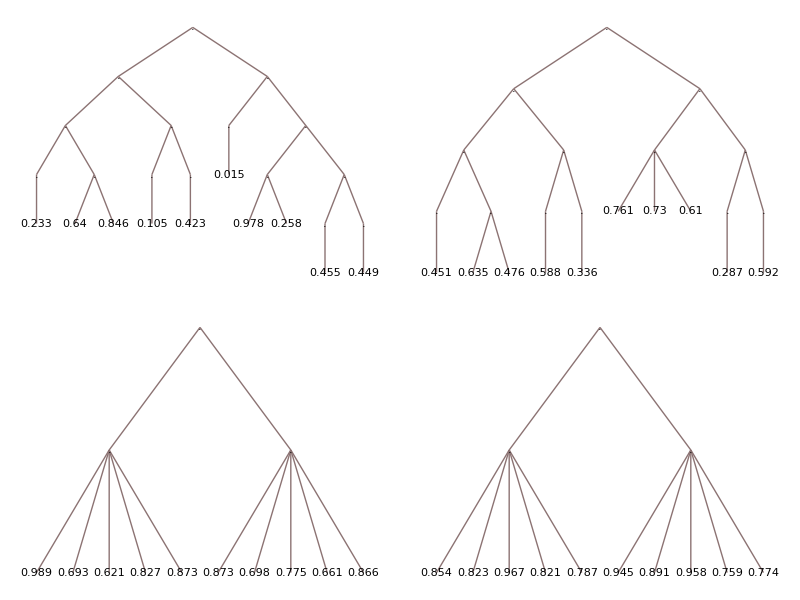

```mathematica
plots = Map[ExampleTree[#,10]&,{0,0.25,0.5,0.75,0.9}]; 
grid=Grid[Partition[plots,3]]
```

```mathematica
lower = 0.2; 
n = 10; 
x =Table[Random[UniformDistribution[{lower,1}]],{n}] ;
tree = RecursiveSplit[x];
```

```mathematica
q1 = 0.2; 
q2 = 0.4
```

0.4

```mathematica
1/q1 + 1/q2
```

7.5

```mathematica
1/(q1*q2)
```

12.5

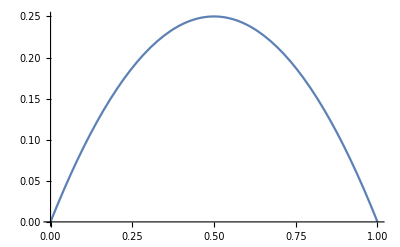

```mathematica
Plot[q*(1-q),{q,0,1}]
```